```mathematica
SetDirectory[NotebookDirectory[]];
Off[NDSolve::"ndsz",NDSolve::maxit,NDSolve::"noout"]
$PlotTheme=None;
Clear["Global`*"];
```

NOTE: Interactive additions are in the section titled "INTERACTIVE PLAYGROUND (Manipulate)". Use Ctrl+F and search for "TrajectoryPlayground". Evaluate that cell to open the sliders and extra plots.

### KERR GEOMETRY

The Kerr metric describes the spacetime geometry around a rotating mass M and angular momentum paramLabeleter a . It is given in Boyer-Lindquist coordinates .

#### Metric Components :

```mathematica
M=1;
SigmaK[r_,θ_]:= r^2 + a^2 Cos[θ]^2;
DeltaK[r_, θ_]:= r^2 - 2 M r + a^2;
```

#### Metric tensor components :

and (off - diagonal, identical) :

```mathematica
gCovTT[r_,θ_]:=-(1-(2M r)/SigmaK[r,θ]);
gCovTPhi[r_,θ_]:=-(2 r M a Sin[θ]^2)/SigmaK[r,θ];
gCovPhiPhi[r_,θ_]:=(r^2+a^2+(2  M r a^2)/SigmaK[r,θ] Sin[θ]^2)Sin[θ]^2;
gCovRR[r_,θ_]:=SigmaK[r,θ]/DeltaK[r,θ];
gCovThTh[r_,θ_]:= SigmaK[r,θ];
```

#### Inverse Metric tensor components:

and  (off - diagonal, identical) :

```mathematica
gConTT[r_,θ_]:=-1/DeltaK[r,θ](r^2+a^2+(2  M r a^2)/SigmaK[r,θ] Sin[θ]^2);
gConTPhi[r_,θ_]:=-(2 M a r)/(DeltaK[r,θ] SigmaK[r,θ]);

gConPhiPhi[r_,θ_]:=(DeltaK[r,θ]- a^2 Sin[θ]^2)/(DeltaK[r,θ]SigmaK[r,θ] Sin[θ]^2);
gConRR[r_,θ_]:=DeltaK[r,θ]/SigmaK[r,θ];
gConThTh[r_,θ_]:=1/SigmaK[r,θ];
```

### Electromagnetic Four-Potential

For a Kerr black hole in a uniform magnetic field , the potential  is given for the Wald solution:

#### Components:

These expressions for  and  involve the interaction between the magnetic field and the rotating spacetime geometry, incorporating the frame-dragging effects.

```mathematica
AtWald[r_,θ_]:=B gCovTPhi[r,θ];
APhiWald[r_,θ_]:=B gCovPhiPhi[r,θ];
```

### Effective Potential for Charged Particles

Defining an effective potential,  helps identify circular orbits and the energy of a charged particle . We combine the metric and electromagnetic potential into auxiliary functions  to solve for the energy .

```mathematica
coefA[r_,θ_,Lz_]:=-gConTT[r,θ];
coefB[r_,θ_,Lz_]:=2(gConTPhi[r,θ](Lz-APhiWald[r,θ])-gConTT[r,θ]AtWald[r,θ]);
coefC[r_,θ_,Lz_]:=-gConPhiPhi[r,θ](Lz-APhiWald[r,θ])^2-gConTT[r,θ] AtWald[r,θ]^2+2gConTPhi[r,θ]AtWald[r,θ](Lz-APhiWald[r,θ])-1;
VeffCh[r_,θ_,Lz_]:=(-coefB[r,θ,Lz]+√(coefB[r,θ,Lz]^2-4coefA[r,θ,Lz]coefC[r,θ,Lz]))/(2coefA[r,θ,Lz]);
```

### ISCO, SPECIFIC E & L FOR KERR

```mathematica
kerrEE[r_,s_]:=(1-2/r+s/r^(3/2))/(√(1-3/r+2s/r^(3/2)));
kerrLL[r_,s_]:=(r^(1/2)-2s/r+s^2/r^(3/2))/(√(1-3/r+2s/r^(3/2)));

Z1Kerr[s_] := 1+(1-s^2)^(1/3)((1+s)^(1/3)+(1-s)^(1/3));
Z2Kerr[s_]:=√(3 s^2+Z1Kerr[s]^2);

rISCOm[s_] := 3 + Z2Kerr[s] - √((3 - Z1Kerr[s])(3 + Z1Kerr[s] + 2 Z2Kerr[s]));
rISCOp[s_] :=  3 + Z2Kerr[s] + √((3 - Z1Kerr[s])(3 + Z1Kerr[s] + 2 Z2Kerr[s]));

rMBm[s_]:=2-s+2 √(1-s);rMBp[s_]:=2+s+2 √(1+s);
rPHm[s_]:=2(1+Cos[2/3 ArcCos[-s]]);
rPHp[s_]:=2(1+Cos[2/3 ArcCos[+s]]);
rHorizon[s_]:=1+√(1-s^2);
```

### COORDINATE TRANSFORMS

```mathematica
xCyl[r_, ϕ_] := r Cos[ϕ];
yCyl[r_, ϕ_] := r Sin[ϕ];

xCart[r_, θ_, ϕ_] := r Sin[θ] Cos[ϕ];
yCart[r_, θ_, ϕ_] := r Sin[θ] Sin[ϕ];
zCart[r_, θ_, ϕ_] := r Cos[θ];
```

### HAMILTONIAN EQUATIONS & NUMERICAL SOLVER

```mathematica
SolveTrajectory[rinit_,θinit_,Lz_,xEND_]:=(
Clear[r,pr,θ, pθ,ϕ];

EE=VeffCh[rinit,θinit,Lz];
Print["a=",a,"  B=",B,"  Lz=",Lz,"  E=",EE];

Hgeo[r_,θ_,pr_,pθ_]:=1/2 gConRR[r,θ] pr^2+1/2 gConThTh[r,θ] pθ^2+1/2+
    1/2( gConTT[r,θ](-EE-AtWald[r,θ])^2+2gConTPhi[r,θ](-EE-AtWald[r,θ])(Lz-APhiWald[r,θ])+gConPhiPhi[r,θ](Lz-APhiWald[r,θ])^2);

DrHgeo[r_,θ_,pr_,pθ_]:=D[Hgeo[r,θ,pr,pθ],r];
DθHgeo[r_,θ_,pr_,pθ_]:=D[Hgeo[r,θ,pr,pθ],θ];
HInvariant=Hgeo[r[τ],θ[τ],pr[τ],pθ[τ]];

eom ={
r'[τ]   ==    gConRR[r[τ] ,θ[τ]]pr[τ],pr'[τ]  == -DrHgeo[r[τ],θ[τ],pr[τ],pθ[τ]],
θ'[τ]   ==   gConThTh[r[τ] ,θ[τ] ]pθ[τ],pθ'[τ]  ==-DθHgeo[r[τ],θ[τ],pr[τ],pθ[τ]],
ϕ'[τ]   ==   -gConTPhi[r[τ] ,θ[τ]]EE+ gConPhiPhi[r[τ] ,θ[τ]]Lz-gConTPhi[r[τ] ,θ[τ]]AtWald[r[τ],θ[τ]]-gConPhiPhi[r[τ] ,θ[τ]]APhiWald[r[τ],θ[τ]]  
};
ics ={r[0]==rinit, pr[0]==0,θ[0]==θinit, pθ[0]==0,ϕ[0]==0};


step0=10^-4;
Switch[numMethod,
1,
methodChoice={"StiffnessSwitching", 
Method->{ {"Projection", Method->{"ExplicitRungeKutta","DifferenceOrder"->9},"Invariants"->HInvariant},Automatic}};,
2,step0=10^-4;methodChoice={"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4}};,
_,methodChoice=Automatic
];

solTraj=NDSolve[{eom,ics},{r,pr,θ,pθ,ϕ},{τ,0, xEND},
  {Method->{"EventLocator","Event"->{r[τ]-rStopH,r[τ]-rStopInf},
     "EventAction":>{Throw[ Null,"StopIntegration"],Throw[Null, "StopIntegration"]},"Method"->methodChoice},
   {StartingStepSize->step0,MaxSteps->∞}}];
ipub= r/.solTraj[[1,1]];tauDomain=ipub["Domain"];{tau0,tau1} = tauDomain[[1]];
Print["tau0=",tau0,"  tau1=",tau1];


);
```

### TRAJECTORY PLOTTER

```mathematica
PlotTrajectory[colour_]:=(
ϕinit=0;
GraphicsGrid[
 {{pic1=ParametricPlot[ {xCart[r[τ],θ[τ],ϕ[τ]], yCart[r[τ],θ[τ],ϕ[τ]] }/.solTraj,{τ,tau0,tau1},PlotStyle->{colour},
     Frame->True,BaseStyle->fontyW,PlotRange->range2D,Prolog->{LightGray,Disk[{0,0},rH]},
     Epilog->{PointSize[0.02],Point[{xCart[rinit,θinit,ϕinit],yCart[rinit,θinit,ϕinit]}]},FrameLabel->{"x","y"},RotateLabel->False,
     Axes->False,ImageSize->ImSz],
pic2=ParametricPlot[ {xCart[r[τ],θ[τ],ϕ[τ]],zCart[r[τ],θ[τ],ϕ[τ]] }/.solTraj,{τ,tau0,tau1},PlotStyle->{colour},
  Frame->True,BaseStyle->fontyW,PlotRange->range2D,Prolog->{LightGray,Disk[{0,0},rH]},
  FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,
 Epilog->{PointSize[0.02],Point[{xCart[rinit,θinit,ϕinit],zCart[rinit,θinit,ϕinit]}],
    Text[Row[{"r_0≐",Round[rinit,0.01],"| θ_0≐",Round[θinit,0.01]}],Scaled[{0.5,0.1}]],
    Text[Row[{"E≐",Round[EE,0.01]," | L≐",Round[Lz,0.01]}],Scaled[{0.5,0.9}]]
}],
pic3=Show[
ContourPlot[VeffCh[√(xx^2+zz^2),ArcTan[zz,xx],Lz]==EE,{xx,0,range1D[[2]]},{zz,range1D[[1]]/2,range1D[[2]]/2},
  ContourStyle->{{Red,Thick,Dotted}},Frame->True,BaseStyle->fontyW,FrameLabel->{"x","z"},AspectRatio->1,
  Frame->True,RotateLabel->False,Axes->False,ImageSize->ImSz,
  Epilog->{LightGray,Disk[{0,0},rH],Black,PointSize[0.02],Point[{xCart[rinit,θinit,ϕinit],zCart[rinit,θinit,ϕinit]}]}],
ParametricPlot[{xCart[r[τ],θ[τ],0],zCart[r[τ],θ[τ],0] }/.solTraj,{τ,tau0,tau1},PlotStyle->{colour}]
],
pic4=Show[ParametricPlot3D[{ xCart[r[τ],θ[τ],ϕ[τ]], yCart[r[τ],θ[τ],ϕ[τ]],  zCart[r[τ],θ[τ],ϕ[τ]] }/.solTraj,
    {τ,tau0,tau1},PlotRange->range3D,BoxStyle->{Black},PlotStyle->{colour},ViewPoint->{0,-3,1},
    Ticks->None,ImageSize->ImSz],
  Graphics3D[{{Black,Text[Style[paramLabel,fontyW],{0,0.5range1D[[1]],1range1D[[1]]}]},{LightGray,Sphere[{0,0,0},rH]},
     {Black,PointSize[0.02],Point[{xCart[rinit,θinit,ϕinit],yCart[rinit,θinit,ϕinit],zCart[rinit,θinit,ϕinit]}]}}],Lighting->"Neutral"]
}},Spacings->0,ImageSize->1000]
);
```

```mathematica
fonty=15;fontyW={FontSize->15,Background->White};ImSz=250;
range1D={-10.5,10.5};range2D={range1D,range1D};range3D={range1D,range1D,range1D};

rH=rHorizon[s];rStopH=rH+10^-2;rStopInf=1000;numMethod=1;
```

### INTERACTIVE PLAYGROUND (Manipulate)

Use the sliders to explore the orbit. Tip: if it is slow, lower Ï.84max and/or turn off the ergosphere surface.

```mathematica
ClearAll[rErgo, SolveTrajectoryData, HConstraint, PoincareSection, TrajectoryPlayground];

(* Stationary limit surface (outer ergosphere), M=1 *)
rErgo[th_, a_] := 1 + Sqrt[1 - a^2 Cos[th]^2];

(* Solve + return everything in an Association (Print suppressed) *)
SolveTrajectoryData[r0_, th0_, Lz0_, tauMax0_, a0_, B0_, method0_: 1] :=
 Module[{sol, t0, t1, E0, rH0},
  Block[{a = a0, B = B0, numMethod = method0, rH, rStopH, rStopInf, Print = (Null &)},
   rH = rHorizon[a];
   rStopH = rH + 10^-2;
   rStopInf = 1000;
   SolveTrajectory[r0, th0, Lz0, tauMax0];
   sol = solTraj; t0 = tau0; t1 = tau1; E0 = EE; rH0 = rH;
  ];
  <|"sol" -> sol, "tau0" -> t0, "tau1" -> t1, "E" -> E0, "rH" -> rH0,
    "a" -> a0, "B" -> B0, "Lz" -> Lz0, "r0" -> r0, "th0" -> th0|>
 ];

(* Hamiltonian constraint (should stay ~0) *)
HConstraint[t_, dat_] := Module[
  {sol = dat["sol"], a0 = dat["a"], B0 = dat["B"], E0 = dat["E"], Lz0 = dat["Lz"],
   rIF, thIF, prIF, pthIF},
  rIF = (r /. sol[[1]]);
  thIF = (θ /. sol[[1]]);
  prIF = (pr /. sol[[1]]);
  pthIF = (pθ /. sol[[1]]);
  Block[{a = a0, B = B0},
    1/2 gConRR[rIF[t], thIF[t]] prIF[t]^2 +
    1/2 gConThTh[rIF[t], thIF[t]] pthIF[t]^2 +
    1/2 +
    1/2 ( gConTT[rIF[t], thIF[t]] (-E0 - AtWald[rIF[t], thIF[t]])^2
        + 2 gConTPhi[rIF[t], thIF[t]] (-E0 - AtWald[rIF[t], thIF[t]]) (Lz0 - APhiWald[rIF[t], thIF[t]])
        + gConPhiPhi[rIF[t], thIF[t]] (Lz0 - APhiWald[rIF[t], thIF[t]])^2 )
  ]
];

(* PoincarÃ© section: crossings of Î¸ = Ï.80/2 (equatorial plane) *)
PoincareSection[dat_, n_: 800, direction_: 1] := Module[
  {sol = dat["sol"], t0 = dat["tau0"], t1 = dat["tau1"], rIF, thIF, prIF,
   ts, vals, pairs, sgn, intervals, roots, goodRoots},
  rIF = (r /. sol[[1]]);
  thIF = (θ /. sol[[1]]);
  prIF = (pr /. sol[[1]]);
  ts = Subdivide[t0, t1, n];
  vals = (thIF /@ ts) - Pi/2;
  pairs = Partition[ts, 2, 1];
  sgn = Sign[Most[vals]]*Sign[Rest[vals]];
  intervals = Pick[pairs, sgn, -1];

  roots = Quiet@Table[
    Check[
      t /. FindRoot[thIF[t] - Pi/2, {t, intervals[[k, 1]], intervals[[k, 2]]}, Method -> "Brent"],
      Nothing
    ],
    {k, Length[intervals]}
  ];

  goodRoots = If[direction == 1, Select[roots, thIF'[#] > 0 &], Select[roots, thIF'[#] < 0 &]];
  ({rIF[#], prIF[#]} & /@ goodRoots)
];

TrajectoryPlayground[] := DynamicModule[
  {parOld = {}, dat = <||>, u = 0., view = "Orbit", poiPts = {}, poiOld = {}},
  Manipulate[
    Module[
      {par, ok, sol, t0, t1, Ï.84clip, Ï.84curve, eps,
       rIF, prIF, thIF, pthIF, phiIF, E0, rH0,
       maxR, range1D, range2D, range3D,
       xy, xz, xyz, ptXY, ptXZ, pt3,
       plotXY, plotXZ, plot3D, plotPot, plotDiag, plotPoincare, ergoSurf,
       Ï.84s, Hvals, Hmax},

      par = {aVal, BVal, r0, Î¸0, LzVal, Ï.84max, method};

      If[par =!= parOld,
        dat = SolveTrajectoryData[r0, Î¸0, LzVal, Ï.84max, aVal, BVal, method];
        parOld = par;
        u = 0.;
        poiPts = {};
        poiOld = {};
      ];

      ok = AssociationQ[dat] && KeyExistsQ[dat, "sol"] && ListQ[dat["sol"]] && dat["sol"] =!= {} && dat["sol"] =!= $Failed;
      If[!ok, Return[Style["Integration failed. Try smaller Ï.84max or different parameters.", Red]]];

      sol = dat["sol"]; t0 = dat["tau0"]; t1 = dat["tau1"]; E0 = dat["E"]; rH0 = dat["rH"];
      If[!(NumericQ[t0] && NumericQ[t1] && t1 > t0),
        Return[Style["No valid Ï.84 domain returned (Ï.841 â.89¤ Ï.840). Try different parameters or smaller Ï.84max.", Red]]
      ];

      maxR = 1.1 Max[r0, 2 rH0, 6];
      range1D = {-maxR, maxR};
      range2D = {range1D, range1D};
      range3D = {range1D, range1D, range1D};

      (* Extract the InterpolatingFunctions by name (robust) *)
      rIF = (r /. sol[[1]]);
      prIF = (pr /. sol[[1]]);
      thIF = (θ /. sol[[1]]);
      pthIF = (pθ /. sol[[1]]);
      phiIF = (ϕ /. sol[[1]]);
      If[Head[phiIF] =!= InterpolatingFunction, phiIF = (φ /. sol[[1]])];

      If[!And @@ (Head[#] === InterpolatingFunction & /@ {rIF, prIF, thIF, pthIF, phiIF}),
        Return[Style["Solution does not contain InterpolatingFunctions for {r, pr, Î¸, pÎ¸, Ï.95}. (Symbol mismatch.)", Red]]
      ];

      Ï.84clip = t0 + u (t1 - t0);
      Ï.84curve = t1;

      xy[t_?NumericQ] := {xCart[rIF[t], thIF[t], phiIF[t]], yCart[rIF[t], thIF[t], phiIF[t]]};
      xz[t_?NumericQ] := {xCart[rIF[t], thIF[t], phiIF[t]], zCart[rIF[t], thIF[t], phiIF[t]]};
      xyz[t_?NumericQ] := {xCart[rIF[t], thIF[t], phiIF[t]], yCart[rIF[t], thIF[t], phiIF[t]], zCart[rIF[t], thIF[t], phiIF[t]]};

      ptXY = Quiet@Check[xy[Ï.84clip], {}];
      ptXZ = Quiet@Check[xz[Ï.84clip], {}];
      pt3  = Quiet@Check[xyz[Ï.84clip], {}];

      plotXY = Show[
        ParametricPlot[Evaluate[xy[Ï.84]], {Ï.84, t0, Ï.84curve},
          Frame -> True, RotateLabel -> False, Axes -> False,
          BaseStyle -> fontyW, PlotRange -> range2D, ImageSize -> ImSz, PlotStyle -> Thick
        ],
        Graphics[{
          LightGray, Disk[{0, 0}, rH0],
          If[showPoint && Length[ptXY] == 2 && VectorQ[ptXY, NumericQ], {Black, PointSize[0.02], Point[ptXY]}, {}]
        }]
      ];

      plotXZ = Show[
        ParametricPlot[Evaluate[xz[Ï.84]], {Ï.84, t0, Ï.84curve},
          Frame -> True, RotateLabel -> False, Axes -> False,
          BaseStyle -> fontyW, PlotRange -> range2D, ImageSize -> ImSz, PlotStyle -> Thick
        ],
        Graphics[{
          LightGray, Disk[{0, 0}, rH0],
          If[showPoint && Length[ptXZ] == 2 && VectorQ[ptXZ, NumericQ], {Black, PointSize[0.02], Point[ptXZ]}, {}]
        }]
      ];

      ergoSurf = If[showErgo,
        ParametricPlot3D[
          With[{re = rErgo[th, aVal]},
            {xCart[re, th, ph], yCart[re, th, ph], zCart[re, th, ph]}
          ],
          {th, 0, Pi}, {ph, 0, 2 Pi},
          Mesh -> None, PlotPoints -> 25,
          PlotStyle -> Directive[Opacity[0.15], LightGray],
          BoundaryStyle -> None
        ],
        Graphics3D[{}]
      ];

      plot3D = Show[
        ParametricPlot3D[Evaluate[xyz[Ï.84]], {Ï.84, t0, Ï.84curve},
          PlotRange -> range3D, BoxStyle -> {Black}, Ticks -> None,
          ImageSize -> 2 ImSz, PlotPoints -> 200
        ],
        Graphics3D[{Opacity[0.25], LightGray, Sphere[{0, 0, 0}, rH0]}],
        ergoSurf,
        If[showPoint && Length[pt3] == 3 && VectorQ[pt3, NumericQ], Graphics3D[{Black, PointSize[0.02], Point[pt3]}], Graphics3D[{}]],
        Lighting -> "Neutral", ViewPoint -> {0, -3, 1}
      ];

      plotPot = Show[
        ContourPlot[
          Block[{a = aVal, B = BVal},
            VeffCh[Sqrt[xx^2 + zz^2], ArcTan[zz, xx], LzVal] == E0
          ],
          {xx, 0, range1D[[2]]}, {zz, range1D[[1]], range1D[[2]]},
          ContourStyle -> {Red, Thick},
          Frame -> True, RotateLabel -> False, Axes -> False,
          BaseStyle -> fontyW, ImageSize -> 2 ImSz
        ],
        ParametricPlot[
          Evaluate[{xCart[rIF[Ï.84], thIF[Ï.84], 0], zCart[rIF[Ï.84], thIF[Ï.84], 0]}],
          {Ï.84, t0, Ï.84curve}, PlotStyle -> Thick
        ],
        Graphics[{LightGray, Disk[{0, 0}, rH0]}]
      ];

      plotDiag = Module[{Ï.84s0, Hvals0, Hmax0},
        Ï.84s0 = Subdivide[t0, t1, 250];
        Hvals0 = Quiet@Table[HConstraint[Ï.84s0[[k]], dat], {k, Length[Ï.84s0]}];
        Hmax0 = Max[Abs[Hvals0]];
        Grid[
          {{
            Plot[rIF[Ï.84], {Ï.84, t0, t1},
              Frame -> True, Axes -> False, BaseStyle -> fontyW, ImageSize -> ImSz,
              FrameLabel -> {"Ï.84", "r(Ï.84)"}
            ],
            Plot[thIF[Ï.84], {Ï.84, t0, t1},
              Frame -> True, Axes -> False, BaseStyle -> fontyW, ImageSize -> ImSz,
              FrameLabel -> {"Ï.84", "Î¸(Ï.84)"}
            ]
          },
          {
            ListLinePlot[Transpose[{Ï.84s0, Hvals0}],
              Frame -> True, Axes -> False, BaseStyle -> fontyW, ImageSize -> 2 ImSz,
              FrameLabel -> {"Ï.84", "H(Ï.84)"},
              PlotRange -> All,
              PlotLabel -> Row[{"max|H| = ", NumberForm[Hmax0, 3]}]
            ],
            SpanFromLeft
          }},
          Spacings -> {2, 1}
        ]
      ];

      plotPoincare = If[poiOld =!= par,
        poiPts = Quiet@Check[PoincareSection[dat, nP, dir], {}];
        poiOld = par;
      ];
      plotPoincare = Show[
        ListPlot[poiPts,
          Frame -> True, Axes -> False, BaseStyle -> fontyW, ImageSize -> 2 ImSz,
          PlotRange -> All, PlotStyle -> Black,
          FrameLabel -> {"r", "pr"}
        ],
        Graphics[Text[Row[{"# points = ", Length[poiPts]}], Scaled[{0.75, 0.9}]]]
      ];

      Switch[view,
        "Orbit", Column[{Row[{plotXY, Spacer[10], plotXZ}], plot3D}, Spacings -> 1],
        "Potential", plotPot,
        "Diagnostics", plotDiag,
        "Poincare", plotPoincare,
        _, plotXY
      ]
    ],

    {{view, "Orbit", "View"}, {"Orbit", "Potential", "Diagnostics", "Poincare"}},
    Delimiter,
    {{aVal, 0.5, "a"}, 0, 0.99, 0.01, Appearance -> "Labeled", ContinuousAction -> False},
    {{BVal, 0.1, "B"}, 0, 1, 0.01, Appearance -> "Labeled", ContinuousAction -> False},
    {{r0, 5, "r0"}, 2.1, 30, 0.1, Appearance -> "Labeled", ContinuousAction -> False},
    {{Î¸0, 1, "Î¸0"}, 0.2, 2.94, 0.01, Appearance -> "Labeled", ContinuousAction -> False},
    {{LzVal, 3.5, "Lz"}, -10, 10, 0.05, Appearance -> "Labeled", ContinuousAction -> False},
    {{Ï.84max, 800, "Ï.84max"}, 50, 2000, 50, Appearance -> "Labeled", ContinuousAction -> False},
    {{method, 1, "Method"}, {1 -> "Projection RK", 2 -> "FixedStep RK", 3 -> "Automatic"}},

    Delimiter,
    {{u, 0, "orbit progress"}, 0, 1, Animator, AnimationRunning -> False},
    {{showPoint, True, "Show moving point"}, {True, False}},
    {{showErgo, False, "Show ergosphere"}, {True, False}},

    Delimiter,
    {{nP, 800, "PoincarÃ© samples"}, 200, 2000, 200, Appearance -> "Labeled", ContinuousAction -> False},
    {{dir, 1, "Crossing dir"}, {1 -> "up", -1 -> "down"}},

    ControlPlacement -> Left,
    SaveDefinitions -> True,
    SynchronousUpdating -> False
  ]
];
```

```mathematica
TrajectoryPlayground[]
```

```mathematica
s=0.5;
a=s;
B=0.1;
tauMax=800;
paramLabel=Row[{"a=",a," | ℬ =",B}];(* initial position and ang.mom. L *) 
rinit=5;
θinit=1;
Lz=3.5;
SolveTrajectory[rinit,θinit,Lz,tauMax];PlotTrajectory[Pink]
```

a=0.5  B=0.1  Lz=3.5  E=0.864329

tau0=0.  tau1=800.

-Graphics-

### PROJECT TOOLKIT

Batch runs, saving/export, and a tiny test set.

```mathematica
ClearAll[
  KerrProjectVersion,
  KerrDefaultParams,
  KerrMakeParams,
  KerrRun,
  KerrRunSummary,
  KerrFunctions,
  KerrTrajectoryTable,
  KerrMinMax,
  KerrOrbitType,
  KerrConstraintStats,
  KerrPoincareCount,
  KerrSummary,
  KerrScan1D,
  KerrScan2D,
  KerrScanDataset,
  KerrExportTrajectoryCSV,
  KerrBLToCartesian,
  KerrOrbitPlot3D,
  KerrOrbitPlotXY,
  KerrTimeSeriesPlot,
  KerrPoincarePlot,
  KerrScanPlot1D,
  KerrSaveRun,
  KerrLoadRun,
  KerrClearOutputs,
  KerrWriteProjectSkeleton,
  KerrRunTests
];

KerrProjectVersion = "v13-big+plots";

(* One place for defaults *)
KerrDefaultParams = <|
  "a" -> 0.9,
  "B" -> 0.1,
  "method" -> 1,
  "r0" -> 5,
  "th0" -> Pi/2 - 0.2,
  "Lz" -> 3,
  "tauMax" -> 200,
  "nSample" -> 400,
  "rCaptureTol" -> 10^-2,
  "rEscape" -> 1000
|>;

KerrMakeParams[overrides___Rule] := Join[KerrDefaultParams, Association[overrides]];

(* One run, returns the SolveTrajectoryData result + the params we used *)
KerrRun[par_Association] := Module[{dat},
  dat = SolveTrajectoryData[
    par["r0"], par["th0"], par["Lz"], par["tauMax"], par["a"], par["B"], par["method"]
  ];
  Join[dat, <|"params" -> par|>]
];

(* Safe access to interpolating functions inside dat *)
KerrFunctions[dat_Association] := Module[{sol, phiIF},
  If[!AssociationQ[dat] || !KeyExistsQ[dat, "sol"], Return[$Failed]];
  sol = dat["sol"];
  If[!ListQ[sol] || sol === {} || sol === $Failed, Return[$Failed]];

  (* robust phi name (ϕ vs φ) *)
  phiIF = (ϕ /. sol[[1]]);
  If[Head[phiIF] =!= InterpolatingFunction, phiIF = (φ /. sol[[1]])];

  <|
    "t" -> (t /. sol[[1]]),
    "r" -> (r /. sol[[1]]),
    "th" -> (θ /. sol[[1]]),
    "phi" -> phiIF,
    "pr" -> (pr /. sol[[1]]),
    "pth" -> (pθ /. sol[[1]])
  |>
];

KerrTrajectoryTable[dat_Association, n_Integer: 500] := Module[{f, t0, t1, ts},
  f = KerrFunctions[dat];
  If[f === $Failed, Return[$Failed]];
  t0 = dat["tau0"]; t1 = dat["tau1"];
  ts = Subdivide[t0, t1, n];
  Table[
    <|
      "tau" -> ts[[k]],
      "t" -> f["t"][ts[[k]]],
      "r" -> f["r"][ts[[k]]],
      "th" -> f["th"][ts[[k]]],
      "phi" -> f["phi"][ts[[k]]],
      "pr" -> f["pr"][ts[[k]]],
      "pth" -> f["pth"][ts[[k]]]
    |>,
    {k, Length[ts]}
  ]
];

KerrMinMax[dat_Association, n_Integer: 400] := Module[{f, t0, t1, ts, rVals, thVals},
  f = KerrFunctions[dat];
  If[f === $Failed, Return[$Failed]];
  t0 = dat["tau0"]; t1 = dat["tau1"];
  ts = Subdivide[t0, t1, n];
  rVals = f["r"] /@ ts;
  thVals = f["th"] /@ ts;
  <|
    "rMin" -> Min[rVals], "rMax" -> Max[rVals],
    "thMin" -> Min[thVals], "thMax" -> Max[thVals]
  |>
];

KerrOrbitType[dat_Association] := Module[{f, rEnd, par, tol, rEsc},
  f = KerrFunctions[dat];
  If[f === $Failed, Return["fail"]];
  par = dat["params"];
  tol = par["rCaptureTol"];
  rEsc = par["rEscape"];
  rEnd = f["r"][dat["tau1"]];
  Which[
    rEnd <= dat["rH"] + tol, "capture",
    rEnd >= rEsc - tol, "escape",
    True, "bound"
  ]
];

KerrConstraintStats[dat_Association, n_Integer: 200] := Module[{t0, t1, ts, vals},
  If[DownValues[HConstraint] === {}, Return[$Failed]];
  t0 = dat["tau0"]; t1 = dat["tau1"];
  ts = Subdivide[t0, t1, n];
  vals = Quiet[HConstraint[#, dat] & /@ ts];
  vals = Select[vals, NumericQ];
  If[vals === {}, Return[$Failed]];
  <|
    "HabsMax" -> Max[Abs[vals]],
    "HabsMean" -> Mean[Abs[vals]],
    "n" -> Length[vals]
  |>
];

KerrPoincareCount[dat_Association, n_Integer: 400, dir_Integer: 1] := Module[{pts},
  If[DownValues[PoincareSection] === {}, Return[$Failed]];
  pts = PoincareSection[dat, n, dir];
  If[!ListQ[pts], Return[$Failed]];
  Length[pts]
];

KerrSummary[dat_Association] := Module[{par, mm, typ, hc, nPoi},
  par = dat["params"];
  mm = KerrMinMax[dat, par["nSample"]];
  typ = KerrOrbitType[dat];
  hc = KerrConstraintStats[dat, Floor[par["nSample"]/2]];
  nPoi = KerrPoincareCount[dat, par["nSample"], 1];
  <|
    "type" -> typ,
    "E" -> dat["E"],
    "a" -> par["a"], "B" -> par["B"], "Lz" -> par["Lz"], "r0" -> par["r0"], "th0" -> par["th0"],
    "rMin" -> Lookup[mm, "rMin", Missing["na"]],
    "rMax" -> Lookup[mm, "rMax", Missing["na"]],
    "HabsMax" -> If[AssociationQ[hc], Lookup[hc, "HabsMax", Missing["na"]], Missing["na"]],
    "HabsMean" -> If[AssociationQ[hc], Lookup[hc, "HabsMean", Missing["na"]], Missing["na"]],
    "nPoincare" -> If[nPoi === $Failed, Missing["na"], nPoi]
  |>
];

(* Fast scans: store only params + summary (no big sol) *)
KerrRunSummary[par_Association] := Module[{dat, sum},
  dat = KerrRun[par];
  sum = KerrSummary[dat];
  <|"params" -> par, "summary" -> sum|>
];

KerrScan1D[base_Association, key_String, vals_List] := Table[
  KerrRunSummary[Join[base, <|key -> v|>]],
  {v, vals}
];

KerrScan2D[base_Association, key1_String, vals1_List, key2_String, vals2_List] := Table[
  KerrRunSummary[Join[base, <|key1 -> v1, key2 -> v2|>]],
  {v1, vals1}, {v2, vals2}
];

KerrScanDataset[scan_] := Dataset[scan /. <|"params" -> p_, "summary" -> s_|> :> Join[p, s]];

KerrExportTrajectoryCSV[dat_Association, file_String, n_Integer: 500] := Module[{tbl, header, rows},
  tbl = KerrTrajectoryTable[dat, n];
  If[tbl === $Failed, Return[$Failed]];
  header = {"tau", "t", "r", "th", "phi", "pr", "pth"};
  rows = (Lookup[#, header] & /@ tbl);
  Export[file, Prepend[rows, header], "CSV"]
];

KerrSaveRun[dat_Association, file_String] := Export[file, dat, "MX"];
KerrLoadRun[file_String] := Import[file, "MX"];

(* Clean outputs before GitHub *)
KerrClearOutputs[] := Module[{nb, cells},
  nb = EvaluationNotebook[];
  cells = Cells[nb, CellStyle -> "Output"];
  NotebookDelete[cells];
];

(* Optional: write a simple folder skeleton for a full repo *)
KerrWriteProjectSkeleton[root_String] := Module[{dir, nbfile, readme},
  dir = ExpandFileName[root];
  CreateDirectory[dir, CreateIntermediateDirectories -> True];
  CreateDirectory[FileNameJoin[{dir, "notebooks"}], CreateIntermediateDirectories -> True];
  CreateDirectory[FileNameJoin[{dir, "data"}], CreateIntermediateDirectories -> True];
  CreateDirectory[FileNameJoin[{dir, "runs"}], CreateIntermediateDirectories -> True];

  nbfile = FileNameJoin[{dir, "notebooks", "KerrBH_TrajectoryPlayground.nb"}];
  Quiet@Check[NotebookSave[EvaluationNotebook[], nbfile], Null];

  readme = StringRiffle[{
    "# KerrBH Trajectory Playground",
    "",
    "Open the notebook and evaluate from the top.",
    "",
    "Main entry:",
    "  TrajectoryPlayground[]",
    "",
    "Project helpers:",
    "  KerrMakeParams[...]",
    "  KerrRun[params]",
    "  KerrSummary[run] // Dataset",
    "  KerrScanDataset[scan]",
    "  KerrExportTrajectoryCSV[run, \"file.csv\"]"
  }, "
"];

  Export[FileNameJoin[{dir, "README.md"}], readme, "Text"];
  dir
];

(* Very small tests. Slow tests are optional. *)
KerrRunTests[slow_: False] := Module[{tests = {}},
  AppendTo[tests,
    VerificationTest[rHorizon[0], 2, TestID -> "rHorizon a=0"]
  ];
  AppendTo[tests,
    VerificationTest[Chop[rHorizon[0.5] - (1 + Sqrt[1 - 0.5^2])], 0, TestID -> "rHorizon formula"]
  ];
  AppendTo[tests,
    VerificationTest[
      NumericQ[Block[{a = 0.9, B = 0.1}, VeffCh[5, Pi/2, 3]]],
      True,
      TestID -> "VeffCh numeric"
    ]
  ];

  If[TrueQ[slow],
    AppendTo[tests,
      VerificationTest[
        AssociationQ[SolveTrajectoryData[5, Pi/2, 3, 20, 0.9, 0.1, 1]],
        True,
        TestID -> "SolveTrajectoryData quick"
      ]
    ];
  ];

  TestReport[tests]
];


(* ----------------------------- *)
(* PLOTS (quick visuals)         *)
(* ----------------------------- *)

KerrBLToCartesian[r_, th_, phi_] := {r Sin[th] Cos[phi], r Sin[th] Sin[phi], r Cos[th]};

KerrOrbitPlot3D[dat_Association, opts___?OptionQ] := Module[{f, t0, t1},
  f = KerrFunctions[dat];
  If[f === $Failed, Return[$Failed]];
  t0 = dat["tau0"]; t1 = dat["tau1"];
  ParametricPlot3D[
    Evaluate@KerrBLToCartesian[f["r"][tau], f["th"][tau], f["phi"][tau]],
    {tau, t0, t1},
    PlotRange -> All,
    BoxRatios -> 1,
    AxesLabel -> {"x", "y", "z"},
    opts
  ]
];

KerrOrbitPlotXY[dat_Association, opts___?OptionQ] := Module[{f, t0, t1},
  f = KerrFunctions[dat];
  If[f === $Failed, Return[$Failed]];
  t0 = dat["tau0"]; t1 = dat["tau1"];
  ParametricPlot[
    Evaluate@Take[KerrBLToCartesian[f["r"][tau], f["th"][tau], f["phi"][tau]], 2],
    {tau, t0, t1},
    PlotRange -> All,
    AspectRatio -> 1,
    AxesLabel -> {"x", "y"},
    opts
  ]
];

KerrTimeSeriesPlot[dat_Association, what_String: "r", opts___?OptionQ] := Module[{f, t0, t1, g},
  f = KerrFunctions[dat];
  If[f === $Failed, Return[$Failed]];
  t0 = dat["tau0"]; t1 = dat["tau1"];
  g = Switch[what,
    "t", f["t"],
    "r", f["r"],
    "th", f["th"],
    "phi", f["phi"],
    "pr", f["pr"],
    "pth", f["pth"],
    _, Return[$Failed]
  ];
  Plot[
    g[tau],
    {tau, t0, t1},
    PlotRange -> All,
    AxesLabel -> {"tau", what},
    opts
  ]
];

KerrPoincarePlot[dat_Association, n_Integer: 800, dir_Integer: 1, opts___?OptionQ] := Module[{pts},
  If[DownValues[PoincareSection] === {}, Return[$Failed]];
  pts = PoincareSection[dat, n, dir];
  If[!ListQ[pts], Return[$Failed]];
  If[pts === {},
    Return@Graphics[
      {Text[Style["No Poincare points: orbit never crosses theta = Pi/2. Try th0 != Pi/2.", 14], Scaled[{0.5, 0.5}]]},
      PlotRange -> {{0, 1}, {0, 1}}, Frame -> True, Axes -> False
    ]
  ];
  ListPlot[
    pts,
    PlotRange -> All,
    AspectRatio -> 1,
    AxesLabel -> {"r", "pr"},
    opts
  ]
];

KerrScanPlot1D[scan_List, xKey_String, yKey_String: "rMin", opts___?OptionQ] := Module[{pts},
  pts = Cases[
    scan,
    <|"params" -> p_Association, "summary" -> s_Association|> :> {p[xKey], s[yKey]},
    Infinity
  ];
  If[pts === {}, Return[$Failed]];
  ListLinePlot[
    pts,
    PlotRange -> All,
    AxesLabel -> {xKey, yKey},
    opts
  ]
];
```

-Graphics3D-

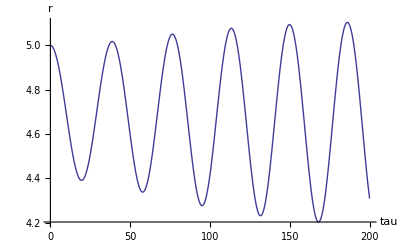

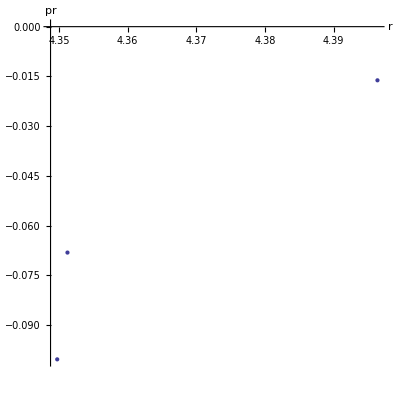

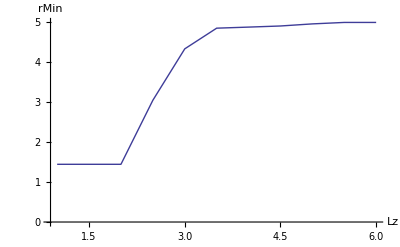

TestReportObject[…]

```mathematica
(* QUICK START *)
par = KerrMakeParams[];
run = KerrRun[par];

KerrSummary[run] // Dataset

(* plots *)
KerrOrbitPlot3D[run]
KerrTimeSeriesPlot[run, "r"]
KerrPoincarePlot[run]

(* 1D scan example (changes only Lz) *)
base = KerrMakeParams["tauMax" -> 80, "nSample" -> 200];
scan = KerrScan1D[base, "Lz", Range[1, 6, 0.5]];
KerrScanDataset[scan]
KerrScanPlot1D[scan, "Lz", "rMin"]

(* tests *)
KerrRunTests[]
```